# Weighted fiber + GRIN

-Graphics-

[1] L. Huo, J. Xi, Y. Wu, and X. Li, “Forward-viewing resonant fiber-optic scanning endoscope of appropriate scanning speed for 3D OCT imaging.,” Opt. Express, vol. 18, no. 14, pp. 14375–14384, 2010.

Note: The scanner is approximated to be a fiber connected to a rigid metallic cylinder!

### Input Parameters

```mathematica
LGRIN = 2.08*10^-3;  (*[m] Length of GRIN lens*)
DGRIN = 0.35*10^-3;  (*[m] Diameter of GRIN lens *)
```

```mathematica
Ltot = 4.5*10^-3;  (*[m] Total Length of the scanning tip: fiber + GRIN*)
```

### Mechanical Data

```mathematica
D1 = 80*10^-6;  (*[m]*)
ρ1 = 2203; (*[kg/m^3]*) (*seibel2006*)
E1 = 73.1*10^9; (*[Pa]*) (*seibel2006*)
A1 = (D1/2)^2*π;
I1 = π/4*(D1/2)^4; (*[m^4]*)
L1 = Ltot-LGRIN;
D2 = DGRIN;
ρ2 = 2203; (*[kg/m^3]*) 
E2 = 73.1*10^9; (*[Pa]*) 
A2 = (D2/2)^2*π;
I2 = π/4*(D2/2)^4; (*[m^4]*)
L2 = LGRIN;
```

### Approximated Resonant Frequency

Asuming concentrated load in the center of gravity of the GRIN lens:

```mathematica
freqs = Table[
L1 = Ltot-LGRIN/2;
L2 = LGRIN;
kcant = (3π)/4*(E1*(D1/2)^4)/L1^3;
weight = ρ2*(D2/2)^2*π*L2;
f = 1/(2π)√(kcant/weight)
,{Ltot,3*10^-3,10*10^-3,0.1*10^-3}];
```

```mathematica
l= Range[3,10,0.1];
```

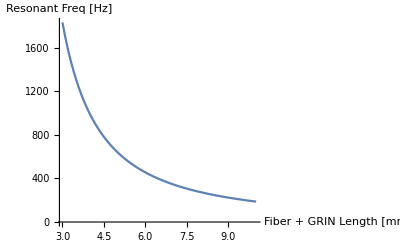

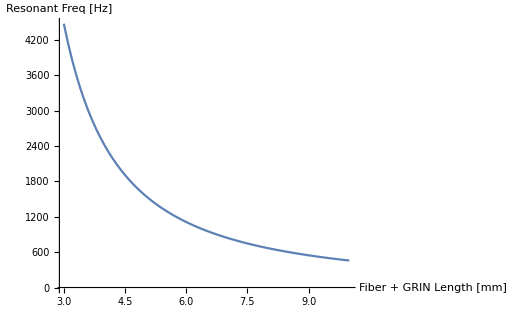

```mathematica
ListLinePlot[Thread[{l,freqs}],PlotRange->Automatic,AxesLabel->{"Fiber + GRIN Length [mm]","Resonant Freq [Hz]"}]
```

### Bending Beam

```mathematica
length = 4.5*10^-3;
Cd = 150*10^-6;
```

```mathematica
k1=1.875; (*meinert2013*)
bendingLine[x_,L_]:=-Cd*(Cos[k1*x/L]-Cosh[k1*x/L]-0.734*(Sin[k1*x/L]-Sinh[k1*x/L]));
```

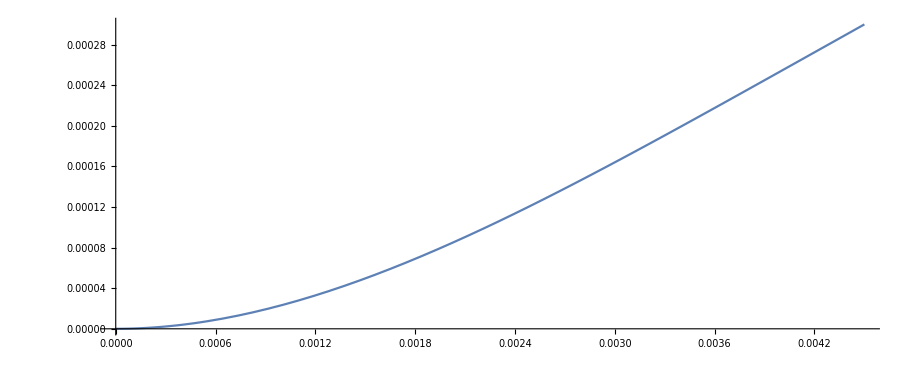

```mathematica
Plot[{bendingLine[x,length]},{x,0,length},AspectRatio->Automatic]
```

```mathematica
angle[x_,L_]:=(180/π)*ArcTan[D[bendingLine[x,length],x]];
```

```mathematica
tipAngle=angle[x,length]/.{x->length}
```

5.24412